## Plot for best-case scenario

Fixed parameter values : kappa = 0.2, beta = 0.5, delta = 0.5, fmax=6.

## Import Data

```mathematica
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
raw=Import["export_data/sensi_anal/temp_min.mat"];
```

## Image Options

```mathematica
(* time ticks *)
timeTicks=Table[{50(i-1),1800+50(i-1)},{i,1,13}];

(* imgs size *)
imgs=350;
(* aspect ratio *)
aratio=0.6;
(* legend position (scaled) *)
legendPos={0.2,0.7};
(* labels (alphabet) *)
labels=Alphabet[];
(* label position (scaled) *)
labelPos={0.05,0.91};
(* bold label on off *)
bold=1;
```

```mathematica
{padLeft,padRight,padBottom,padTop}={50,30,40,20};  (* image padding *)
```

```mathematica
(* time plot range *)
plRange={100,400};
(* social plot range *)
plRangeSoc={-0.02,1.05};
(* emissions plot range *)
plRangeEm={-0.5,18.5};
(* temperature plot range *)
plRangeTemp={-0.1,5.3};
```

```mathematica
(* varying parameter values *)
deltaVals={0,0.5,1,1.5,2,3};
kappaVals={0.01,0.02,0.05,0.1,0.2,100};
```

```mathematica
(* colour of shading *)
shade1=Directive[Opacity[0.5],Lighter[TMBcolours⟦1⟧,0.8]];
shade2=Directive[Opacity[0.5],Lighter[TMBcolours⟦3⟧,0.8]];
```

```mathematica
(* generic plot options *)
opts={PlotStyle->{TMBcolours⟦1⟧,shade1,shade1,TMBcolours⟦3⟧,shade2,shade2},
Filling->{2->{{1},shade1},
3->{{1},shade1},
5->{{4},shade2},
6->{{4},shade2}},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}};
```

## Kappa Plots

### Break up data

```mathematica
(* max_temp data split *)
tSeries = raw[[1,1]];
socSeries = raw[[1,2;;]];
emissionSeries=raw[[2,2;;]];
tempSeries=raw[[3,2;;]];
```

### Make Plots

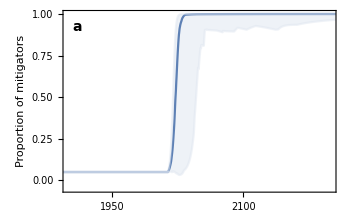

```mathematica
(* proportion of mitigators *)
socPlot=ListLinePlot[{Transpose[{tSeries,socSeries[[2]]}],
Transpose[{tSeries,socSeries[[1]]}],
Transpose[{tSeries,socSeries[[3]]}]},
PlotRange->{plRange,{-0.05,1}},
opts,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[1]],14,If[bold==1,Bold]],Scaled[labelPos]],
FrameLabel->{{"Proportion of mitigators",None},{None,None}}]
```

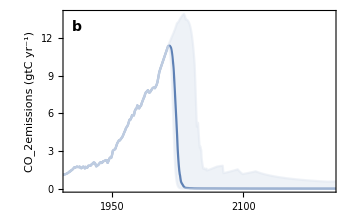

```mathematica
(* emissions *)
emissionPlot=ListLinePlot[{Transpose[{tSeries,emissionSeries[[2]]}],
Transpose[{tSeries,emissionSeries[[1]]}],
Transpose[{tSeries,emissionSeries[[3]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[2]],14,If[bold==1,Bold]],Scaled[labelPos]],
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{None,None}}]
```

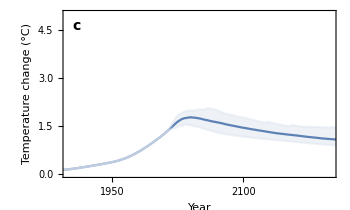

```mathematica
(* temperature plot *)
tempPlot=ListLinePlot[{Transpose[{tSeries,tempSeries[[2]]}],
Transpose[{tSeries,tempSeries[[1]]}],
Transpose[{tSeries,tempSeries[[3]]}]},
PlotRange->{plRange,{0,5}},
opts,
Epilog->Text[Style[labels[[3]],14,If[bold==1,Bold]],Scaled[labelPos]],
FrameLabel->{{"Temperature change (°C)",None},{"Year",None}}]
```

## Plot Grid

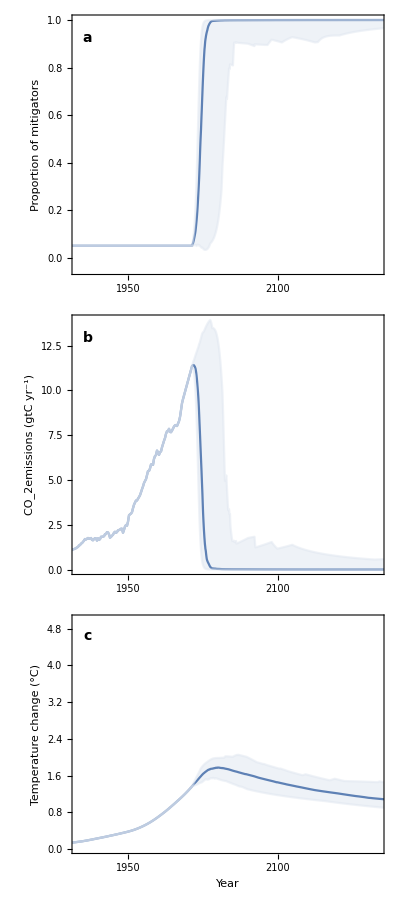

```mathematica
plotGrid=Grid[{{socPlot},{emissionPlot},{tempPlot}},Spacings->{-2.4,-2.2}]
```

```mathematica
Export["figures/sensi_Tmin.png",plotGrid,ImageResolution->200];
```